## Roads and Wheels

### RollingSquare

```mathematica
RollingSquare::usage = "RollingSquare[(opts)] generates a list animation of a rolling square.";
Movie::usage= "Movie is an option to RollingSquare and similar functions that specifies whether a movie, or just the final image, should be shown.";
Frames::usage= "Frames is an option to RollingSquare and similar functions that specifies the number of frames that define the output, whether movie or single image.";
LastWheelOnly::usage = "LastWheelOnly is an option to RollingSquare that controls, when a still image is shown, whether all wheels are shown, or only the last one.";
TracePoints::usage = "TracePoints is an option to RollingSquare that controls whether the locus of a vertex is shown.";
WheelColor::usage = "WheelColor is an option to RollingSquare that sets the color of the square wheel.";CenterPointSize::usage = "CenterPointSize is an option to RollingSquare that sets the size of the central point on the wheel.";
CornerPointSize::usage = "CornerPointSize is an option to RollingSquare that sets the size of the corner point on the wheel.";
TracePointSize::usage = "TracePointSize is an option to RollingSquare that sets the size of the points on the locus.";BorderStyle::usage = "BorderStyle is an option to RollingSquare that sets the style of the border of the wheel.";

Options[RollingSquare] = {Movie->True, Frames->30, BorderStyle->Thickness[0.003], WheelColor->Gray, CenterPointSize->PointSize[0.015], LastWheelOnly->True,TracePoints->True,TracePointSize->PointSize[0.015],CornerPointSize->PointSize[0.015]};

RollingSquare[n_:4,opts___]:= Module[
{mov, rotate, cr, ir, npts=30,dots = {tracesize},a, plot,startpolygon, polygon},
{movQ, npts, bsty, wcol, centersize, cornersize, tracesize, trQ,lastonlyQ} = {Movie, Frames, BorderStyle, WheelColor,CenterPointSize,CornerPointSize, TracePointSize, TracePoints,LastWheelOnly} /. {opts} /. Options[RollingSquare];
cr = Csc[π/n];	(* circumradius of polygon *)  
ir = Cot[π/n];	(* inradius of polygon *)   
a = ir*ArcSinh[1/ir];

rotate[p_, t_, center_] :=RotationTransform[-t, center][p];

plot = Show[Table[Plot[cr - ir Cosh[(x - 2 a i)/ir], 
      {x, -a + 2 a i, a + 2 a i},
    Evaluate[Sequence@@FilterRules[{opts}, (First /@ Options[Plot])]],PlotRange->All,PlotPoints->50,  PlotStyle->{Black,Thickness[0.004]}], {i, 0, 6}]];

startpolygon = N@Map[# + {0, cr} &, Map[{Re[#], Im[#]} &,cr N[Exp[I Range[-π/2 + π/n, 3 π/2 + π/n, 2 π/n]]]]];
polygons={};
polygon[tVal_] := Module[{loop=N[Floor[(t + a)/(2a)]]},(* loop tells which loop the square is on *) 
Map[{tVal,0} + rotate[#,loop 2π/n + ArcTan[Sinh[(tVal-loop 2 a)/ir]], {0,cr}]&,startpolygon]];


images = Table[newpolygon = polygon[t]; 
AppendTo[polygons, {EdgeForm[bsty], FaceForm[wcol],Polygon[newpolygon],
			Line[{newpolygon⟦{1,3}⟧,newpolygon⟦{2,4}⟧}],
centersize,Point[{t, cr}],
        {cornersize,Point[newpolygon[[n]]]}}];
	AppendTo[dots, Point[newpolygon[[n]]]];
		Show[Graphics[{ Thickness[.0005], If[lastonlyQ,polygons[[-1]] , polygons],
        If[trQ,dots,{}],
Line[{{-cr, cr}, {13 a,cr}}]}, Sequence@@FilterRules[{opts}, (First /@ Options[Graphics])]], plot,
    PlotRange->{{-cr, 13.2 a }, {-.2, 2 cr + .15}}], {t, If[npts==1, 11 a, 0.],11a, 11 a/If[npts==1,1,(npts-1)]}];
If[!movQ, Show[images[[-1]]],ListAnimate[images]]];
```

Preface

Building a wheel

Suppose we are given a road in the form of a rectifiable curve in the lower half - plane parametrized by f (t) = (x (t), y (t)), where x (t) is increasing, x (0) = 0, y (t) < 0. By the wheel corresponding to the road we mean a curve that will roll smoothly on the road. More precisely, a wheel will be a curve given by a polar function r = r (θ) such that the axle of the wheel, which initially is at (0, 0), stays on the x - axis directly above the wheel - road contact point as the curve rolls along the road. The wheel' s axle may or may not coincide with the wheel' s geometric center. The road is assumed to provide enough friction so that there is never any slipping of the wheel. The rolling motion can be described by a function θ=θ (t) that describes the amount of angular rotation for the wheel to roll from f (0) to f (t).
                                                                                                -Graphics-

These functions must satisfy the following conditions : 
1. Initial condition. The initial contact point is at f(0), directly under the origin, whence θ(0) = -π/2.
2. Rolling condition. The amount unravelled on the wheel matches the distance travelled on the road: ∀ t, the arc length of f between f(0) and f(t) equals the arc length of the polar curve between θ(0) and θ(t). 
3. Radius condition. The radius of the wheel matches the depth of the road at the corresponding point: For any t, r(θ(t)) = - y(t).

The key to getting a wheel is finding the function θ(t), since the radius condition will then yield r(θ).
The first two conditions become a simple differential equation, which can lead to either a closed-form description of θ or a numerical approximation. The rolling condition is:

∫_0^t √((ⅆx/ⅆt)^2+(ⅆy/ⅆt)^2)ⅆt=∫_(-π/2)^θ[t] √((r)^2+(ⅆr/ⅆθ)^2)ⅆθ
   And, we have ⅆr/ⅆθ ⅆθ/ⅆt=-ⅆy/ⅆt(obtained by differentiating the radius condition)
So, we get these:
                          ⅆθ/ⅆt=-ⅆx/ⅆt 1/y[t] , θ[0]=-π/2 , r[θ[t]]=-y[t]

#### Remarks

Closed-form solutions

Suppose the road y =f(x) is periodic with period a. Then the corresponding wheel does not necessarily close up on itself to form a topological disk . The condition for such closure-the closed-wheel condition is that there exists a rational number k so that 2πk = θ(a)-θ(0) =∫_0^a-1/(f(x))ⅆx. If k = 1/n, n a positive integer, then the wheel rolls over n periods of the road during each complete revolution. As an example, consider the road given by y = d + cos x,        
                                                                                                     -Graphics-
The wheel for a cosine road given by - 3.5 + cos x winds around endlessly without closing because 3.5 is not one of the special values √(1+n^2).                                                            Let’s do the integrate:

```mathematica
Integrate[-1/(d+Cos[x]),{x,0,2π},Assumptions->d<-1]
```

Polygonal wheel

The roads corresponding to polygonal wheels are derived from the case of a wheel that is nothing more than a straight line. 
Consider the polar equation r = - Csc(θ), - π< θ < 0, whose graph is a horizontal line one unit below the x-axis.
The results above show that the road on which this polar line will roll is given by y =f(x) = -r(θ(x)) where θ(0)= - π/2

```mathematica
Clear[x];ClearAll[θ];θ[x]/.First[DSolve[{θ'[x]==-Sin[θ[x]],θ[0]==-π/2},θ[x],x]]//Quiet
```

```mathematica
θ[x_]=-2 ArcCot[ⅇ^x];y=Csc[θ[x]]//Simplify
```

But in fact,  y = -Cosh[x]

```mathematica
FunctionExpand[Csc[2 ArcCot[ⅇ^x]],x∈Reals]//FullSimplify
```

```mathematica
Plot[-Cosh[t-2 ArcSinh[1] Quotient[t+ArcSinh[1], 2 ArcSinh[1]]],{t,-5,4π},PlotRange->{{-5, 12}, {-7, 4.5}} ,
FrameTicks->{Range[-5,10,5], Range[-6, 4, 2], {},{}},
ImagePadding->15,ImageSize->500,Frame->True, Axes->True,GridLines->{{},{0}}]
```

How about n-gon? Particularly, think about triangle?

```mathematica
Plot[-Cosh[t-2 ArcSinh[Tan[π/3]] Quotient[t+ArcSinh[Tan[π/3]],2 ArcSinh[Tan[π/3]]]],{t,-5,4π},PlotRange->{{-5, 12}, {-7, 4.5}} ,
FrameTicks->{Range[-5,10,5], Range[-6, 4, 2], {},{}},
ImagePadding->15,ImageSize->500,Frame->True, Axes->True,GridLines->{{},{0}}]
```

n-gon

```mathematica
Plot[{θ[x]+π/2,y},{x,-2,2},GridLines->Table[{ArcSinh[Tan[π/n]],π/n},{n,4.,10.,2.}]ᵀ]
```

Important Discussion

As we shall see several times in this paper, the depth of a road plays a crucial role in determining the shape of the wheel. If the catenary road y = - cosh x is raised or lowered, the shape of the wheel changes. Consider the family of roads k - cosh x where k < 1. If k = 0, then the wheel is a straight line, but other values of k yield radically different wheels.

```mathematica
Clear/@{k,x,ϕ,θ,r};
Integrate[-1/(-Cosh[t]+k),{t,0,x},Assumptions->k<1&&x>0]
```

```mathematica
ϕ[x_,k_]:=(2 ArcTan[((1+k) Tanh[x/2])/(√(1-k^2))])/(√(1-k^2));
θ[x_,k_]:=ϕ[x,k]-π/2;θ[x_,-1]=Limit[θ[x,k],{k->-1}];
r[x_,k_]:=-k+Cosh[x];
```

```mathematica
Grid[Partition[Table[Show[{ParametricPlot[{r[t,k]Cos[θ[t,k]],r[t,k]Sin[θ[t,k]]},{t,-2,2}],Plot[k-Cosh[x],{x,-2,2}]},PlotRange->{{-2,2},{-4,1}},AxesOrigin->{0,0}],{k,{-1,0,0.7,0.9}}],2]]
```

Presentation in Mathematica

```mathematica
θSol[f_, {tmin_, tmax_}]:=θSol[f]=θ[t]/.First[NDSolve[{θ[0]==-π/2,θ'[t]==-1/f[[2]]},θ[t],{t,tmin,tmax}]];
road[yfunc_] :=road[yfunc]=Plot[yfunc,{t,-10,30},PlotStyle->{Red,Thick},PlotPoints->100];
cc=ⅇ^(π/4)-1;
vee[x_] :=-Sign[x] x - 1;
lab[-Cosh[t-2 ArcSinh[1] Quotient[t+ArcSinh[1], 2 ArcSinh[1]]]]="extension of -cosh x";
lab[Cos[t]-Sqrt[1+4]]="cos(x) - √5";
lab[Cos[t]-Sqrt[1+9]]="cos(x) - √10";
lab[Cos[t]-2]="cos(x) - 2";
lab[-Cosh[t]]="-cosh x";
lab[-t^2-1/4]="-x^2-1/4";
lab[-Cosh[t-2 ArcSinh[Tan[π/3]] Quotient[t+ArcSinh[Tan[π/3]],2 ArcSinh[Tan[π/3]]]]]="extension of -cosh x";
lab[vee[t-2 cc Quotient[t+cc, 2 cc]]]="extension of ±x - 1";
```

```mathematica
Manipulate[
{tmin, tmax}=Which[f===-Cosh[t], {-4,4},f===-t^2-1/4, {-4,4}, True,  { -20,30}];
If[f===-Cosh[t], xval = Max[Min[xval, 3],-3]];
If[f===-t^2-1/4, xval = Max[Min[xval, 3],-3]];
θS=θSol[{t,f}, {tmin, tmax}];
transform[pt_, tval_]:= TranslationTransform[{tval,0}][RotationTransform[-π/2-θS/.t->tval][pt]];
Column[{Pane[Style[StringForm["road equation: ``",lab[f]],FontFamily->"Times", 12],Alignment->{Left,Center},ImageSize->{400, 25}];
Show[ParametricPlot[Evaluate[transform[-f {Cos[θS],Sin[θS]}/. t->tt,xval]],{tt,tmin,tmax},PlotStyle->Thick, PlotPoints->50],
road[f],
Graphics[{PointSize[0.018], Point[cen={xval,0}],PointSize[0.015],
tangentPt=-f {Cos[θS],Sin[θS]}/. t-> xval; 
tangentPtOrig={0,f }/. t-> 0; 
Point[transform[tangentPt,xval]],
Point[{xval,0}+RotationTransform[-π/2-θS/.t->xval][tangentPtOrig]],
Line[{cen,transform[ tangentPtOrig,xval]}]}],
PlotRange->{{-5, 12}, {-7, 4.5}} ,
FrameTicks->{Range[-5,10,5], Range[-6, 4, 2], {},{}},
ImagePadding->15,ImageSize->500,Frame->True, Axes->False,GridLines->{{},{0}}]}],
{{xval,0,"position on x axis"},-5.6,8 π}, 
{ {f,-Cosh[t-2 ArcSinh[1] Quotient[t+ArcSinh[1], 2 ArcSinh[1]]],"road shape"},  
{
-Cosh[t-2 ArcSinh[1] Quotient[t+ArcSinh[1], 2 ArcSinh[1]]]->"linked catenaries for square wheel",
-Cosh[t-2 ArcSinh[Tan[π/3]] Quotient[t+ArcSinh[Tan[π/3]],2 ArcSinh[Tan[π/3]]]]->"linked catenaries for triangular wheel",
-Cosh[t]->"catenary: - cosh(x)",
Cos[t]-Sqrt[1+4]->"two-loop cosine: cos(x) - √5",
Cos[t]-Sqrt[1+9]-> "three-loop cosine: cos(x) - √10",
Cos[t]-2 -> "infinite cosine: cos(x) - 2", 
-t^2-1/4->"parabola: -x^2 - 1/4",
vee[t-2 cc Quotient[t+cc, 2 cc]]->"four-loop sawtooth"}, PopupMenu}, 
ControlPlacement->Top, TrackedSymbols->Manipulate, SaveDefinitions->True]
```

Some Codes

### CameraSimulation

```mathematica
CameraSimulation::"usage"="CameraSimulation simulates a photograph of a rolling wheel taken with a stationary camera.";
CameraSimulation:=Module[{norm,f,places,a},norm[v_]:=√(v.v);f[pt_]:=Module[{del=0.02},Table[norm[pt] {Cos[t],Sin[t]},{t,a=ArcTan@@pt-del,a+2 del,del/10}]];Show[Graphics[{AbsolutePointSize[5],Circle[{0,1},1],places={{-0.007241,0.1},{-0.304,0.27},{0.319,0.3},{0.616,0.747},{-0.434,0.739},{0.0434,0.986},{0.514,1.43},{-0.507,1.45},{-0.268,1.64},{0.145,1.76}};(Text["Focus On This!",#1]&)/@Flatten[f/@places,1]}],PlotRange->All,BaseStyle->{FontFamily->"Times",FontSize->9}]];
```

### SpokedBicyclePhotograph

```mathematica
SpokedBicyclePhotograph::usage = "SpokedBicyclePhotograph generates a simulated photograph of a rolling bicycle wheel.";

th = Thickness[0.001];
SpokedBicyclePhotograph := Module[{step,spokes,rims,wheel,g,b},
	step = 0.05;spokes = 20;rims = {};
g = Compile[{x,y}, (Abs[√(x^2 + (y-1)^2) - Cos[3 π/2 - ArcTan[x, y-1]]])/2];
wheel[time_] := Module[{mat={{Cos[time],Sin[time]},{-Sin[time], Cos[time]}}},
     N[{
AppendTo[rims,{th, Table[Circle[{0.,1.},rad],{rad,1,1.1,0.1/2}]}/. 
		  {x_?NumericQ,y_?NumericQ} :>  mat.({x,y}-{0.,1.})+{time,1}];
   {th,Red,Table[
     {b=g[(r+step/2) Cos[s],1+(r+step/2) Sin[s]];
     GrayLevel[Which[ b<0.085, 0, b<0.2,0.5, 
             b<0.5,0.65, b<0.6,0.75,b<0.8,0.8,
            True, 0.85]],Black,Thickness[0.001],
     Line[{{0.,1.}+ r {Cos[s],Sin[s]}, {0,1}+(r+step){Cos[s],Sin[s]}}]},
            {r,0.,1-step,step},{s,0.,2 π,2. π/spokes}]} /. 
            {x_?NumericQ,y_?NumericQ} :>    mat.({x,y}-{0,1})+{time,1}}]  ];
 Show[Graphics[{
{ Thickness[.0013 2],Red, Circle[{0, 1/2}, 1/2-.02],Circle[{0, 1/2}, 1/2+.02]},
 Map[wheel,Range[0.,0.06,0.06/10]],
        rims}], ImageSize->300,PlotRange -> {{-1.3, 1.3}, {-0.3, 2.3}}]]
```

```mathematica
Duangle:=Animate[
Module[{pr,ps,pq,pp,rot,trans,f1,duangle},
{pr,ps,pq,pp}={{-0.75,√3/4},{0.75,√3/4},{0,0},{0,√3/2}};rot=RotationTransform[θ,{0,0}];trans=TranslationTransform[Which[0≤θ≤π/3,(1-Cos[θ]){Cos[π/3],Sin[π/3]},π/3≤θ≤2 π/3,Sin[θ-π/6] {Cos[π/3],Sin[π/3]},(2π)/3≤θ≤π,{Sin[θ-π/6]-1/2,(√3)/2}]];
f1[z_]:=GeometricTransformation[GeometricTransformation[z,rot],trans];
Graphics[{
{RGBColor[0.643137, 0.823529, 0.533333],
EdgeForm[{Gray,Thickness[0.002]}],Triangle[{{-1,0},{1,0},{0,√3}}]},
duangle=N[{Disk[pq,0.5 √3,{π/6,5 π/6}],Disk[pp,0.5 √3,{-5 π/6,-π/6}]}];
f1[Style[duangle,RGBColor[0, 0.835294, 0]]]},PlotRange->{{-1.1,1.1},{-0.5,√3+0.1}},Axes->False
]],{{θ,0, "θ"},0,π}]
```

```mathematica
PerfectSquareHole:= Module[{θ, spokes},
Manipulate[
Module[
{tval,end,rot, translate,line,w,a,b,c,f,rotor,auxcircle, tracepts, circle},
w=2;tval=π/4;r2=w-w/(2 Sin[tval]);
{a,b,c}={{-1,0}, {1,0}, {0, 1 }}; s=2(√2-1);
end=a+√2;
rot=RotationTransform[θ, {0, 1}];
translate= TranslationTransform[Which[
0≤θ≤π/4, -{Cos[θ]+Sin[θ]-1,0},π/4≤θ≤π/2, -{√2-1,- Cos[θ] - Sin[θ]+√2},
π/2≤θ≤3π/4, -{√2-1,- Cos[θ] + Sin[θ]-2+√2},
3π/4≤θ≤π, -{- Cos[θ] +Sin[θ]-1,-2+2 √2},π≤θ≤5π/4, -{ Cos[θ] +Sin[θ]+1,-2+2 √2},
5π/4≤θ≤3π/2, -{-√2+1, -Cos[θ] -Sin[θ]+√2-2},3π/2≤θ≤7π/4, -{ -√2+1,-Cos[θ] +Sin[θ]+√2},

7π/4≤θ≤2π, -{-Cos[θ]+Sin[θ]+1,0}]];
f[z_] := translate[rot[z]];
f1[z_]:=GeometricTransformation[GeometricTransformation[z, rot],translate];
Graphics[{
{RGBColor[0.79,1,0.56],
EdgeForm[{Gray,Thickness[0.002]}],Rectangle[{-1, -(Sqrt[2]-1)},{1, -(Sqrt[2]-1)+2}]},
{White,Rectangle [ (c-{s/2,s}), c+{s/2, 0}]}, 
Red,Thickness[0.002], 
rotor = N[{Circle[c, √2, {-3 π/4,- π/4}],Circle[a, 2, {0, π/4}],
Circle[b, 2, {3π/4,π}],Circle[c, r2, {π/4,3π/4}]}];
auxcircle = Circle[c, r2, {0,2π}];
f1[{Polygon[ {c, c-{0.08,0.2} 0.8, c-0.8 {-0.08, 0.2}}],
 rotor,{Blue,auxcircle},
{Black,Line[{a,c}], Line[ {b,c}],Line[{b,a}],
{Line[ {c,end}],Line[{c,end {-1,1}}],
Line[Table[{c, c+r2 {Cos[tt], Sin[tt]}}, {tt, 0, 15/16  2π , 2π/16}]] }[[If[spokes,3,{1,2}]]]}}],
tracepts=Take[
{c,{1-√2,1},{1-√2,3-2 √2},{√2-1,3-2 √2},{√2-1,1}}, 2+Quotient[θ-π/4, π/2]]; {Thick, Line[tracepts], Line[{tracepts⟦-1⟧, f[c]}]}},ImageSize->300,PlotRange->{{-1.02,1.02}, {-.5,1.72}}]], {{θ,0, "θ"},0,2π},{{spokes,False, "spokes"}, {False,True}},TrackedSymbols->Manipulate, SaveDefinitions->True]]
```

```mathematica
Clear[rot];
 Manipulate[
θ=x /.Degree -> π/180;k=Ceiling[2π/θ];rr=Round[2π/θ];
If[n>2 k(k-1),n=2k(k-1)];
z=θ-(2 π)/k;small=k z;
large=θ-k z;ends=π/2-Prepend[Accumulate[Riffle[Table[large,{k}],Table[small,{k-1}]]], 0];
pieces = Reverse/@ Partition[ends,2,1];
Acolor[j_,i_]:=If[EvenQ[Quotient[i-j,k]],1,0];
Bcolor[j_,i_]:=If[EvenQ[Quotient[i-j,k-1]],1,0];
rot[i_]:=z_Disk | z_Line| z_Circle:>GeometricTransformation[z,RotationTransform[i θ ]];
Apieces=pieces⟦Range[1,2 k-1,2]⟧;
Bpieces=pieces⟦Range[2,2 k-2,2]⟧;
time =If[Abs[2π/θ - rr]<10^-5, 2 rr, 2 k (k-1)];
Column[{Style[StringForm["number of steps to return to start: ``",time], FontFamily->"Times"],
Graphics[{
Table[{EdgeForm[{Thickness[0.017]}],FaceForm[Acolor[j,n]/.{0->Brown,1->White}],Disk[{0,0},1,Apieces⟦j⟧]},{j,k}],

Table[{EdgeForm[{Thickness[0.017]}],FaceForm[Bcolor[j,n]/.{0->Brown,1->White}],Disk[{0,0},1,Bpieces⟦j⟧]},{j,k-1}], 
If[n< If[Abs[2π/θ - rr]<10^-5,2 rr,2 k(k-1)],{Thickness[0.005],Line[{1.1 {Cos[π/2+θ],Sin[π/2+θ]},{0,0},{0,1.1}}],
EdgeForm[{Red, Thickness[0.005]}],FaceForm[{White,Opacity[0.2]}],Disk[{0,0}, 1.1,{π/2,π/2+θ} ]},{}]}/.
rot[n],PlotRange->1.2,ImageSize->300]}],
{{x,π/4, "slice angle, radians"}, 0.1, 2π},
{{x,Pi/4,"slice angle, radians"},{Pi/4->"π / 4",Pi/2->"π / 2",3Pi/2->"3 π / 2",π->"π",185 Degree->"185°",6,1}, SetterBar},


{{n,0, "number of slices"},0,
If[Abs[2π/x - Round[2π/x] /. Degree -> π/180]<10^-5,2 Round[2π/x/. Degree-> π/180],2 Ceiling[(2 π)/x/. Degree->π/180](Ceiling[(2 π)/x/. Degree->π/180]-1)],1,Appearance->"Open"}, TrackedSymbols:>{n,x}]
```

### A Curious Bicycle Track

```mathematica
unitVec[v_]:=v/(√(v.v));

FrontTrack[rear_,t_]:=rear+unitVec[D[rear,t]];
rear={t,Sin[t]+t/10-Cos[t/2]};
```

```mathematica
ParametricPlot[Evaluate[{rear,FrontTrack[rear,t]}],{t,0,3 π},Frame->True,Axes->False,FrameTicks->None,PlotRange->{{1,9},{-1,3}}]
```

```mathematica
f[x_]:=ⅇ^(-1/x);
f[0] =Limit[f[x], x->0];
fder[0][x_]:=f[x];
fder[n_][0]:=Limit[(fder[n-1][h]-fder[n-1][0])/h,h->0];
fder[n_][x_]:=fder[n-1]'[x];
```

```mathematica
fder[5][x]
fder[5][0]
```

ⅇ^(-1/x)/x^10-(20 ⅇ^(-1/x))/x^9+(120 ⅇ^(-1/x))/x^8-(240 ⅇ^(-1/x))/x^7+(120 ⅇ^(-1/x))/x^6

0

```mathematica
Table[fder[n][0],{n,15}]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
finn[1][t_]:={t,ⅇ^(-1/(t(1-t)))};
finn[1][0|0.]={0,0};
finn[1][1|1.]={1,0};
```

```mathematica
ParametricPlot[finn[1][t],{t,0,1},PlotRange->{{0,1},{-.2,.2}},PlotStyle->Thick, Frame->True]
```

```mathematica
Do[finn[i][t_]:=Evaluate[FrontTrack[finn[i-1][t],t]];
finn[i][0|0.]={i-1,0};
finn[i][1|1.]={i,0},{i,2,4}];
```

```mathematica
finn[2][t]
```

{1/(√(1+ⅇ^(-2/((1-t) t)) (1/((1-t) t^2)-1/((1-t)^2 t))^2))+t,ⅇ^(-1/((1-t) t))+(ⅇ^(-1/((1-t) t)) (1/((1-t) t^2)-1/((1-t)^2 t)))/(√(1+ⅇ^(-2/((1-t) t)) (1/((1-t) t^2)-1/((1-t)^2 t))^2))}

```mathematica
Table[Count[finn[i][t],_^_,∞],{i,4}]
```

{3,28,385,6844}

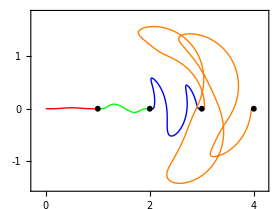

```mathematica
cols={Red,Green,Blue,Orange};
track=Quiet[ParametricPlot[Evaluate[Table[finn[i][t],{i,4}]],{t,0,1},PlotStyle->Table[{Thick,cols⟦i⟧},{i,4}]]];
Show[track,Graphics[{PointSize[0.015],Point[Table[{i,0},{i,4}]]}],Frame->True,Axes->None,PlotRange->{{-0.2,4.2},{-1.5,1.8}},FrameTicks->{Range[0,4],Range[-1,1],None,None}]
```

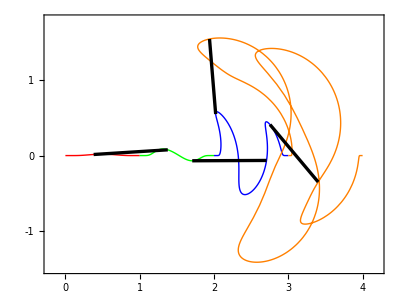

```mathematica
Show[track,Graphics[
{{Thickness[0.006],MapIndexed[Line[{finn[Min[#2⟦1⟧,3]][#1],finn[Min[#2⟦1⟧,3]+1][#1]}]&,{0.38,0.71,0.17, 0.85}]}}],PlotRange->{{-0.2,4.2},{-1.5,1.8}},Axes->False,Frame->True]
```

```mathematica
Manipulate[tt=Floor[t]+1;Show[track,Graphics[{Thickness[0.01],Line[{finn[tt][t-tt+1],finn[tt+1][t-tt+1]}]}],Frame->True,FrameTicks->None,Axes->False,PlotRange->{{-0.2,5},{-2,2}}],{t,0,2.99}]
```

FreeStyle